```mathematica
Integrate[(1-ⅇ^(-2 n/(n-1)a(g-x)))PDF[NormalDistribution[0,√((n-1)/n)],x](g-x)PDF[NormalDistribution[0,1/(√n)],g-x],{x,-∞,g}]
```

ConditionalExpression[1/(2 √((-1+n)/n) π)ⅇ^(-(g^2 n)/2) √n (1/(√2 (2 a-g) n^2)ⅇ^((4 a^2+g^2+4 a g (-1+n))/(2-2 n)) (-1+n) (-ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) (2 a+g (-1+n)) √((-2 a+g)^2/(-1+n)) √π Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+(2 a-g) (√2 (ⅇ^((-2 a+g)^2/(2 (-1+n)))-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))))+ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) √((2 a+g (-1+n))^2/(-1+n)) √π Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)]))-(g^2 (ⅇ^(1/2 g^2 (-1+n)) g^2 √(g^2 (-1+n)) √π Erf[(√(g^2/(-1+n)))/(√2)]+√(g^2/(-1+n)) (-√2 (-1+ⅇ^((g^2 (-2+n) n)/(2 (-1+n)))) √(g^2 (-1+n))+ⅇ^(1/2 g^2 (-1+n)) g^2 (-1+n) √π Erf[(√(g^2 (-1+n)))/(√2)])))/(√2 (g^2/(-1+n))^(3/2) √(g^2 (-1+n)) n^2)+1/(g^2 n^2)ⅇ^(1/2 g^2 (-1+n)) √(g^2 (-1+n)) √(π/2) (√(g^2/(-1+n)) √(g^2 (-1+n)) n Erf[(√(g^2/(-1+n)))/(√2)]+g (g n Erf[(√(g^2 (-1+n)))/(√2)]-√(g^2 (-1+n)) √(n^2/(-1+n)) (-1+Erf[(g n)/(√2 √(n^2/(-1+n)))])))+(√2 √(n^2/(-1+n))-ⅇ^(1/2 g^2 (-1+n)) g n √π+ⅇ^(1/2 g^2 (-1+n)) g n √π Erf[(g n)/(√2 √(n^2/(-1+n)))])/(√2 (n^2/(-1+n))^(3/2))-(ⅇ^((4 a^2-4 a g+g^2 (-1+n)^2)/(2 (-1+n))) g √(π/2) (-(2 a-g) √((2 a+g (-1+n))^2/(-1+n)) √(n^2/(-1+n)) Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+√((-2 a+g)^2/(-1+n)) ((2 a+g (-1+n)) √(n^2/(-1+n)) Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)]-√((2 a+g (-1+n))^2/(-1+n)) n (-1+Erf[((2 a+g (-1+n)) √(n^2/(-1+n)))/(√2 n)]))))/(√((-2 a+g)^2/(-1+n)) √((2 a+g (-1+n))^2/(-1+n)) n √(n^2/(-1+n)))+1/(√2 n^2 √(n^2/(-1+n)))ⅇ^(-(2 a g n)/(-1+n)) (√2 √(n^2/(-1+n))-n (√2 √(n^2/(-1+n))-2 a ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) √π+ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g √π)+ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g n^2 √π-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) (2 a+g (-1+n)) n √π Erf[((2 a+g (-1+n)) √(n^2/(-1+n)))/(√2 n)])),(Re[n^2/(-1+n)]==0&&Re[g n]<0&&Re[((2 a+g (-1+n)) n)/(-1+n)]<0)||(Re[n^2/(-1+n)]≥0&&Re[n^2/(1-n)]<0)]

```mathematica
Simplify[1/(2 √((-1+n)/n) π)ⅇ^(-(g^2 n)/2) √n (1/(√2 (2 a-g) n^2)ⅇ^((4 a^2+g^2+4 a g (-1+n))/(2-2 n)) (-1+n) (-ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) (2 a+g (-1+n)) √((-2 a+g)^2/(-1+n)) √π Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+(2 a-g) (√2 (ⅇ^((-2 a+g)^2/(2 (-1+n)))-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))))+ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) √((2 a+g (-1+n))^2/(-1+n)) √π Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)]))-(g^2 (ⅇ^(1/2 g^2 (-1+n)) g^2 √(g^2 (-1+n)) √π Erf[(√(g^2/(-1+n)))/(√2)]+√(g^2/(-1+n)) (-√2 (-1+ⅇ^((g^2 (-2+n) n)/(2 (-1+n)))) √(g^2 (-1+n))+ⅇ^(1/2 g^2 (-1+n)) g^2 (-1+n) √π Erf[(√(g^2 (-1+n)))/(√2)])))/(√2 (g^2/(-1+n))^(3/2) √(g^2 (-1+n)) n^2)+1/(g^2 n^2)ⅇ^(1/2 g^2 (-1+n)) √(g^2 (-1+n)) √(π/2) (√(g^2/(-1+n)) √(g^2 (-1+n)) n Erf[(√(g^2/(-1+n)))/(√2)]+g (g n Erf[(√(g^2 (-1+n)))/(√2)]-√(g^2 (-1+n)) √(n^2/(-1+n)) (-1+Erf[(g n)/(√2 √(n^2/(-1+n)))])))+(√2 √(n^2/(-1+n))-ⅇ^(1/2 g^2 (-1+n)) g n √π+ⅇ^(1/2 g^2 (-1+n)) g n √π Erf[(g n)/(√2 √(n^2/(-1+n)))])/(√2 (n^2/(-1+n))^(3/2))-(ⅇ^((4 a^2-4 a g+g^2 (-1+n)^2)/(2 (-1+n))) g √(π/2) (-(2 a-g) √((2 a+g (-1+n))^2/(-1+n)) √(n^2/(-1+n)) Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+√((-2 a+g)^2/(-1+n)) ((2 a+g (-1+n)) √(n^2/(-1+n)) Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)]-√((2 a+g (-1+n))^2/(-1+n)) n (-1+Erf[((2 a+g (-1+n)) √(n^2/(-1+n)))/(√2 n)]))))/(√((-2 a+g)^2/(-1+n)) √((2 a+g (-1+n))^2/(-1+n)) n √(n^2/(-1+n)))+1/(√2 n^2 √(n^2/(-1+n)))ⅇ^(-(2 a g n)/(-1+n)) (√2 √(n^2/(-1+n))-n (√2 √(n^2/(-1+n))-2 a ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) √π+ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g √π)+ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g n^2 √π-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) (2 a+g (-1+n)) n √π Erf[((2 a+g (-1+n)) √(n^2/(-1+n)))/(√2 n)])),n >0]
```

1/(2 √(-1+n) π)ⅇ^(-(g^2 n)/2) n ((√2 √(1/(-1+n))-ⅇ^(1/2 g^2 (-1+n)) g √π+ⅇ^(1/2 g^2 (-1+n)) g √π Erf[g/(√2 √(1/(-1+n)))])/(√2 (1/(-1+n))^(3/2) n^2)+1/(√2 √(1/(-1+n)) n^2)ⅇ^(-(2 a g n)/(-1+n)) (√2 √(1/(-1+n))-√2 √(1/(-1+n)) n+2 a ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) √π-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g √π+ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g n √π-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) (2 a+g (-1+n)) √π Erf[((2 a+g (-1+n)) √(1/(-1+n)))/(√2)])-(ⅇ^((4 a^2-4 a g+g^2 (-1+n)^2)/(2 (-1+n))) g √(π/2) ((-2 a+g) √(1/(-1+n)) √((2 a+g (-1+n))^2/(-1+n)) n Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+√((-2 a+g)^2/(-1+n)) (-√((2 a+g (-1+n))^2/(-1+n)) n (-1+Erf[((2 a+g (-1+n)) √(1/(-1+n)))/(√2)])+(2 a+g (-1+n)) √(1/(-1+n)) n Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)])))/(√(1/(-1+n)) √((-2 a+g)^2/(-1+n)) √((2 a+g (-1+n))^2/(-1+n)) n^2)+1/(√2 (2 a-g) n^2)ⅇ^((4 a^2+g^2+4 a g (-1+n))/(2-2 n)) (-1+n) (-ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) (2 a+g (-1+n)) √((-2 a+g)^2/(-1+n)) √π Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+(2 a-g) (√2 (ⅇ^((-2 a+g)^2/(2 (-1+n)))-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))))+ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) √((2 a+g (-1+n))^2/(-1+n)) √π Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)]))+1/(g^2 n^2)ⅇ^(1/2 g^2 (-1+n)) √(g^2 (-1+n)) √(π/2) (√(g^2/(-1+n)) √(g^2 (-1+n)) n Erf[(√(g^2/(-1+n)))/(√2)]+g (-√(1/(-1+n)) √(g^2 (-1+n)) n (-1+Erf[g/(√2 √(1/(-1+n)))])+g n Erf[(√(g^2 (-1+n)))/(√2)]))-(g^2 (ⅇ^(1/2 g^2 (-1+n)) g^2 √(g^2 (-1+n)) √π Erf[(√(g^2/(-1+n)))/(√2)]+√(g^2/(-1+n)) (-√2 (-1+ⅇ^((g^2 (-2+n) n)/(2 (-1+n)))) √(g^2 (-1+n))+ⅇ^(1/2 g^2 (-1+n)) g^2 (-1+n) √π Erf[(√(g^2 (-1+n)))/(√2)])))/(√2 (g^2/(-1+n))^(3/2) √(g^2 (-1+n)) n^2))

```mathematica
e[g_,n_,a_]:=1/(2 √(-1+n) π)ⅇ^(-(g^2 n)/2) n ((√2 √(1/(-1+n))-ⅇ^(1/2 g^2 (-1+n)) g √π+ⅇ^(1/2 g^2 (-1+n)) g √π Erf[g/(√2 √(1/(-1+n)))])/(√2 (1/(-1+n))^(3/2) n^2)+1/(√2 √(1/(-1+n)) n^2)ⅇ^(-(2 a g n)/(-1+n)) (√2 √(1/(-1+n))-√2 √(1/(-1+n)) n+2 a ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) √π-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g √π+ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) g n √π-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))) (2 a+g (-1+n)) √π Erf[((2 a+g (-1+n)) √(1/(-1+n)))/(√2)])-(ⅇ^((4 a^2-4 a g+g^2 (-1+n)^2)/(2 (-1+n))) g √(π/2) ((-2 a+g) √(1/(-1+n)) √((2 a+g (-1+n))^2/(-1+n)) n Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+√((-2 a+g)^2/(-1+n)) (-√((2 a+g (-1+n))^2/(-1+n)) n (-1+Erf[((2 a+g (-1+n)) √(1/(-1+n)))/(√2)])+(2 a+g (-1+n)) √(1/(-1+n)) n Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)])))/(√(1/(-1+n)) √((-2 a+g)^2/(-1+n)) √((2 a+g (-1+n))^2/(-1+n)) n^2)+1/(√2 (2 a-g) n^2)ⅇ^((4 a^2+g^2+4 a g (-1+n))/(2-2 n)) (-1+n) (-ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) (2 a+g (-1+n)) √((-2 a+g)^2/(-1+n)) √π Erf[(√((-2 a+g)^2/(-1+n)))/(√2)]+(2 a-g) (√2 (ⅇ^((-2 a+g)^2/(2 (-1+n)))-ⅇ^((2 a+g (-1+n))^2/(2 (-1+n))))+ⅇ^((8 a^2+4 a g (-2+n)+g^2 (2-2 n+n^2))/(2 (-1+n))) √((2 a+g (-1+n))^2/(-1+n)) √π Erf[(√((2 a+g (-1+n))^2/(-1+n)))/(√2)]))+1/(g^2 n^2)ⅇ^(1/2 g^2 (-1+n)) √(g^2 (-1+n)) √(π/2) (√(g^2/(-1+n)) √(g^2 (-1+n)) n Erf[(√(g^2/(-1+n)))/(√2)]+g (-√(1/(-1+n)) √(g^2 (-1+n)) n (-1+Erf[g/(√2 √(1/(-1+n)))])+g n Erf[(√(g^2 (-1+n)))/(√2)]))-(g^2 (ⅇ^(1/2 g^2 (-1+n)) g^2 √(g^2 (-1+n)) √π Erf[(√(g^2/(-1+n)))/(√2)]+√(g^2/(-1+n)) (-√2 (-1+ⅇ^((g^2 (-2+n) n)/(2 (-1+n)))) √(g^2 (-1+n))+ⅇ^(1/2 g^2 (-1+n)) g^2 (-1+n) √π Erf[(√(g^2 (-1+n)))/(√2)])))/(√2 (g^2/(-1+n))^(3/2) √(g^2 (-1+n)) n^2))
```

Power::infy: Infinite expression 1/(√(0``-2.8756399370041676)) encountered.

Power::indet: Indeterminate expression (0``-2.8756399370041676)^0. encountered.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -2 √751.

Power::infy: Infinite expression 1/(√(0``-3.176669932668149)) encountered.

Power::indet: Indeterminate expression (0``-3.176669932668149)^0. encountered.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -2 √1001.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -6 √139.

General::stop: Further output of N::meprec will be suppressed during this calculation.

Power::infy: Infinite expression 1/(√(0``-2.1430148002540954)) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::indet: Indeterminate expression (0``-2.1430148002540954)^0. encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

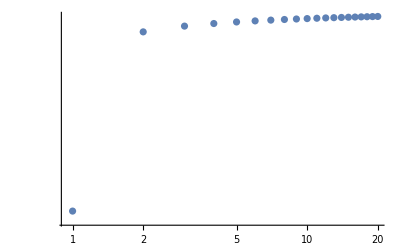

```mathematica
ListLogLogPlot[Table[n e[1,n,1.2]//N,{n,3,10000,500}] ]
```

```mathematica
(a ⅇ^(-g^2/2))/(√(2 π))/. g-> 1 /. a->1.2
```

0.290365

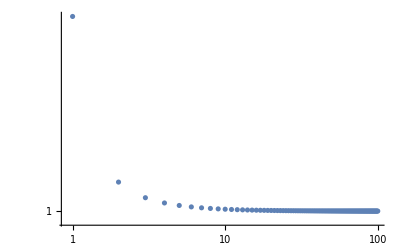

```mathematica
ListLogLogPlot[Table[(n e[1,n,1.8])/((n-1) e[1,n-1,1.8])//N,{n,3,1000,10}] ]
```

```mathematica
f[x_,n_,a_,g_]:=n(1-ⅇ^(-2 n/(n-1)a(g-x)))PDF[NormalDistribution[0,√((n-1)/n)],x](g-x)PDF[NormalDistribution[0,1/(√n)],g-x]If[x < g,1,0]
```

```mathematica
f2[x_,n_,a_,g_]:=n(1-ⅇ^(-2 a(g-x)))PDF[NormalDistribution[0,1],x](g-x)PDF[NormalDistribution[0,1/(√n)],g-x]If[x < g,1,0]
```

```mathematica
f3[x_,n_,a_,g_]:=n(1-ⅇ^(-2 a(g-x)))PDF[NormalDistribution[0,1],x](√n(g-x))/(√(2π))If[x < g,1,0]
```

```mathematica
f4[x_,n_,a_,g_]:=n(1-ⅇ^(-2 a(g-x)))/(√(2π))(g-x)PDF[NormalDistribution[0,1/(√n)],g-x]If[x < g,1,0]
```

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Manipulate[Plot[{f[x,n,a,g],f2[x,n,a,g],f3[x,n,a,g],f4[x,n,a,g]},{x,-3,g+1},PlotRange->{{-1,g+1},{0,2}}],{n,2,1000,1},{a,0.5,3,0.01},{g,0.5,3,0.01}]
```

```mathematica
Manipulate[Plot[{Abs[f[x,n,a,g]-f2[x,n,a,g]]},{x,-3,g+1}],{n,2,10000,100},{a,0.5,3,0.01},{g,0.5,3,0.01}]
```

```mathematica
Plot[Exp[]]
```

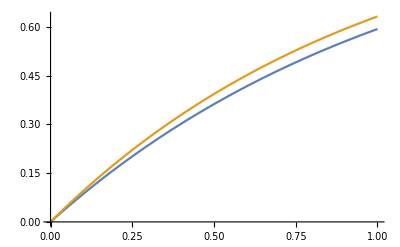

```mathematica
Plot[{1-Exp[-0.9x],1-Exp[-x]},{x,0,1}]
```

```mathematica
Manipulate[Plot[{Abs[f[x,n,a,g]-f2[x,n,a,g]]},{x,-3,g+1}],{n,2,10000,100},{a,0.5,3,0.01},{g,0.5,3,0.01}]
```

```mathematica
Integrate[(1-ⅇ^(-2 a s))PDF[NormalDistribution[0,1],s - g]s PDF[NormalDistribution[0,1/(√n)],s],{s,-∞,0}]
```

ConditionalExpression[(ⅇ^(-g^2/2) √n (ⅇ^((-2 a+g)^2/(2 (1+n))) (2 a-g) (1+Erf[(2 a-g)/(√2 √(1+n))])+ⅇ^(g^2/(2+2 n)) g Erfc[g/(√2 √(1+n))]))/(2 (1+n)^(3/2) √(2 π)),Re[n]≥-1]

```mathematica
e2[n_,a_,g_]:=(ⅇ^(-g^2/2) √n (ⅇ^((-2 a+g)^2/(2 (1+n))) (2 a-g) (1+Erf[(2 a-g)/(√2 √(1+n))])+ⅇ^(g^2/(2+2 n)) g Erfc[g/(√2 √(1+n))]))/(2 (1+n)^(3/2) √(2 π))
```

```mathematica
Integrate[(1-ⅇ^(-2 a s))PDF[NormalDistribution[0,√((n-1)/n)],s - g]s PDF[NormalDistribution[0,1/(√n)],s],{s,-∞,0}]
```

ConditionalExpression[1/(2 √((-1+n)/n) n^(3/2) √(n^2/(-1+n)) √(2 π))ⅇ^((g^2 n)/(2-2 n)) (-2 a ⅇ^((-2 a (-1+n)+g n)^2/(2 (-1+n) n^2))+2 a ⅇ^((-2 a (-1+n)+g n)^2/(2 (-1+n) n^2)) n+ⅇ^(g^2/(2 (-1+n))) g n-ⅇ^((-2 a (-1+n)+g n)^2/(2 (-1+n) n^2)) g n-ⅇ^(g^2/(2 (-1+n))) g n Erf[(g √(n^2/(-1+n)))/(√2 n)]-ⅇ^((-2 a (-1+n)+g n)^2/(2 (-1+n) n^2)) (2 a (-1+n)-g n) Erf[(√(n^2/(-1+n)) (-2 a (-1+n)+g n))/(√2 n^2)]),Re[n^2/(-1+n)]≥0]

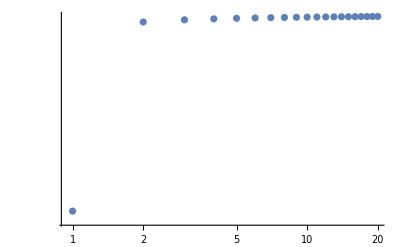

```mathematica
ListLogLogPlot[Table[n e2[n,1.1,1.3]//N,{n,3,10000,500}] ]
```

```mathematica
Limit[n(ⅇ^(-g^2/2) √n (ⅇ^((-2 a+g)^2/(2 (1+n))) (2 a-g) (1+Erf[(2 a-g)/(√2 √(1+n))])+ⅇ^(g^2/(2+2 n)) g Erfc[g/(√2 √(1+n))]))/(2 (1+n)^(3/2) √(2 π)),n-> ∞]
```

(a ⅇ^(-g^2/2))/(√(2 π))

```mathematica
(a ⅇ^(-g^2/2))/(√(2 π))/. a-> 0.3/. g -> 1.3
```

0.0514106

```mathematica
(ⅇ^(-g^2/2) √n (ⅇ^((-2 a+g)^2/(2 (1+n))) (2 a-g) (1+Erf[(2 a-g)/(√2 √(1+n))])+ⅇ^(g^2/(2+2 n)) g Erfc[g/(√2 √(1+n))]))/(2 (1+n)^(3/2) √(2 π))//TeXForm
```

\frac{e^{-\frac{g^2}{2}} \sqrt{n} \left((2 a-g) e^{\frac{(g-2 a)^2}{2 (n+1)}} \left(\text{erf}\left(\frac{2 a-g}{\sqrt{2} \sqrt{n+1}}\right)+1\right)+g
   e^{\frac{g^2}{2 n+2}} \text{erfc}\left(\frac{g}{\sqrt{2} \sqrt{n+1}}\right)\right)}{2 \sqrt{2 \pi } (n+1)^{3/2}}